```mathematica
SetDirectory["C:/Users//grant//Documents/LaserData"];

imf=FileNames["*jpg*"]
prism=FileNames["*30mA*"]
```

{393 20in 31mA ND1.0.jpg,393 40in 31mA ND1.0.jpg,393 60in 31mA ND1.0.jpg,393 76in 31mA ND1.0.jpg,393ND3.6.jpg,393ND4.jpg,397 00in 30mA ND2.0.jpg,397 00in 85.2mA ND4.0.jpg,397 05in 30mA ND2.0.jpg,397 05in 85.2mA ND4.0.jpg,397 10in 30mA ND2.0.jpg,397 10in 85.2mA ND4.0.jpg,397 15in 30mA ND2.0.jpg,397 15in 85.2mA ND4.0.jpg,397 20in 30mA ND2.0.jpg,397 20in 85.2mA ND4.0.jpg,397 25in 30mA ND2.0.jpg,397 25in 85.2mA ND4.0.jpg,397 30in 30mA ND2.0.jpg,397 30in 85.2mA ND4.0.jpg,397 35in 30mA ND2.0.jpg,397 35in 85.2mA ND4.0.jpg,397 40in 30mA ND2.0.jpg,397 40in 85.2mA ND4.0.jpg,397 45in 30mA ND2.0.jpg,397 45in 85.2mA ND4.0.jpg,397 50in 30mA ND2.0.jpg,397 50in 85.2mA ND4.0.jpg,397 55in 30mA ND2.0.jpg,397 55in 85.2mA ND4.0.jpg,397 60in 30mA ND2.0.jpg,397 60in 85.2mA ND4.0.jpg,397 65in 30mA ND2.0.jpg,397 65in 85.2mA ND4.0.jpg,397 70in 30mA ND2.0.jpg,397 70in 85.2mA ND4.0.jpg,397 75in 30mA ND2.0.jpg,397 75in 85.2mA ND4.0.jpg,397 76in 30mA ND2.0.jpg,397 78in 85.2mA ND4.0.jpg,397ND4.2.jpg,397ND4.jpg,397 prism pair test1.jpg,397 prism pair test control far.jpg,397 prism pair test control.jpg,423 20in 29mA ND2+1.jpg,423 40in 29mA ND2+1.jpg,423 60in 29mA ND2+1.jpg,423 76in 29mA ND2+1.jpg,852 20in 35mA ND4.0.jpg,852 40in 35mA ND4.0.jpg,852 60in 35mA ND4.0.jpg,852 76in 35mA ND4.0.jpg,852ND4.3.jpg,852ND4.jpg,852ND4ref.jpg,854 20in 52mA ND2.6.jpg,854 40in 52mA ND2.6.jpg,854 60in 52mA ND2.6.jpg,854 76in 52mA ND2.6.jpg,854ND4.3.jpg,854ND4.6.jpg,854ND4.jpg,854ND5.jpg,866 20in 25mA NoND.jpg,866 20in 34mA ND0.6.jpg,866 40in 25mA NoND.jpg,866 40in 34mA ND0.6.jpg,866 60in 25mA NoND.jpg,866 60in 34mA ND0.6.jpg,866 76in 25mA NoND.jpg,866 76in 34mA ND0.6.jpg,866 78in 34mA ND0.6.jpg,866ND3.5.jpg,866ND3.6.jpg,866ND3abs.jpg,866ND3.jpg,866 no prism far.jpg}

{397 00in 30mA ND2.0.jpg,397 05in 30mA ND2.0.jpg,397 10in 30mA ND2.0.jpg,397 15in 30mA ND2.0.jpg,397 20in 30mA ND2.0.jpg,397 25in 30mA ND2.0.jpg,397 30in 30mA ND2.0.jpg,397 35in 30mA ND2.0.jpg,397 40in 30mA ND2.0.jpg,397 45in 30mA ND2.0.jpg,397 50in 30mA ND2.0.jpg,397 55in 30mA ND2.0.jpg,397 60in 30mA ND2.0.jpg,397 65in 30mA ND2.0.jpg,397 70in 30mA ND2.0.jpg,397 75in 30mA ND2.0.jpg,397 76in 30mA ND2.0.jpg}

```mathematica
(*imdRaw=Import[#,"Data"]&/@imf;//AbsoluteTiming*)
imdRaw=Import[#,"Data"]&/@prism;//AbsoluteTiming
dimensions=Dimensions[imdRaw[[1]]]
xDim=dimensions[[2]];
yDim=dimensions[[1]];
```

{2.8352,Null}

{1200,1600}

```mathematica
nGauss=30;
center=Reverse[Position[GaussianFilter[#,nGauss],Max[GaussianFilter[#,nGauss]]][[1]]]&/@imdRaw
window=500;

x1=Max[{(#[[1]]-window),1}]&/@center;
x2=Min[{(#[[1]]+window),xDim}]&/@center;
y1=Max[{(#[[2]]-window),1}]&/@center;
y2=Min[{(#[[2]]+window),yDim}]&/@center;

x1=Max[{#,1}]&/@x1;
x2=Min[{#,xDim}]&/@x2;
y1=Max[{#,1}]&/@y1;
y2=Min[{#,yDim}]&/@y2;

(*x1=x1-100;
x2=x2-100;*)

imd=Table[Take[imdRaw[[i]],{y1[[i]],y2[[i]]},{x1[[i]],x2[[i]]}],{i,1,Length[imdRaw]}];


Image[#/Max[#]]&/@imd
Image[GaussianFilter[#,nGauss]/Max[GaussianFilter[#,nGauss]]]&/@imd
```

{{545,447},{748,465},{1069,511},{822,564},{1030,593},{861,635},{612,682},{894,712},{849,747},{1086,780},{673,689},{1011,707},{832,745},{923,504},{678,563},{1047,565},{677,605}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{ | Estimate | Standard Error | t-Statistic | P-Value
x0 | 504.835 | 0.467084 | 1080.82 | 0.
wx | 166.029 | 1.04983 | 158.149 | 0.
a | 2956.38 | 15.0237 | 196.781 | 0.
b | 1840.52 | 6.03142 | 305.156 | 0., | Estimate | Standard Error | t-Statistic | P-Value
x0 | 510.724 | 0.381191 | 1339.81 | 0.
wx | 143.064 | 0.836636 | 170.999 | 0.
a | 4225.3 | 20.1528 | 209.663 | 0.
b | 1830.61 | 7.19619 | 254.386 | 0., | Estimate | Standard Error | t-Statistic | P-Value
x0 | 499.839 | 0.20363 | 2454.64 | 0.
wx | 121.41 | 0.438377 | 276.953 | 0.
a | 10133.3 | 30.2057 | 335.476 | 0.
b | 1868.8 | 9.57349 | 195.205 | 0., | Estimate | Standard Error | t-Statistic | P-Value
x0 | 497.765 | 0.159471 | 3121.35 | 0.
wx | 94.3011 | 0.336237 | 280.46 | 0.
a | 11775. | 35.1239 | 335.241 | 0.
b | 1903.12 | 9.39851 | 202.492 | 0., | Estimate | Standard Error | t-Statistic | P-Value
x0 | 497.973 | 0.119584 | 4164.22 | 0.
wx | 72.1479 | 0.248437 | 290.407 | 0.
a | 15832. | 46.0459 | 343.831 | 0.
b | 1933.74 | 10.4318 | 185.369 | 0., | Estimate | Standard Error | t-Statistic | P-Value
x0 | 500.701 | 0.130145 | 3847.25 | 0.
wx | 57.6995 | 0.268027 | 215.275 | 0.
a | 19033.8 | 75.1045 | 253.431 | 0.
b | 1985.66 | 14.9129 | 133.151 | 0., | Estimate | Standard Error | t-Statistic | P-Value
x0 | 498.749 | 0.110602 | 4509.42 | 0.
wx | 51.2513 | 0.226939 | 225.838 | 0.
a | 21809.4 | 82.2302 | 265.224 | 0.
b | 2017.64 | 15.2545 | 132.265 | 0., | Estimate | Standard Error | t-Statistic | P-Value
x0 | 497.085 | 0.0952197 | 5220.4 | 0.
wx | 53.9503 | 0.195676 | 275.712 | 0.
a | 20022.2 | 61.7736 | 324.122 | 0.
b | 2002.45 | 11.8004 | 169.694 | 0., | Estimate | Standard Error | t-Statistic | P-Value
x0 | 497.31 | 0.0951491 | 5226.64 | 0.
wx | 61.4659 | 0.196389 | 312.98 | 0.
a | 17325.3 | 46.9536 | 368.987 | 0.
b | 1934.21 | 9.67258 | 199.969 | 0., | Estimate | Standard Error | t-Statistic | P-Value
x0 | 498.538 | 0.118356 | 4212.17 | 0.
wx | 70.101 | 0.245573 | 285.458 | 0.
a | 14964.8 | 44.3149 | 337.692 | 0.
b | 1885.89 | 9.86754 | 191.121 | 0., | Estimate | Standard Error | t-Statistic | P-Value
x0 | 495.949 | 0.155696 | 3185.36 | 0.
wx | 86.9623 | 0.326609 | 266.258 | 0.
a | 4087.17 | 12.8843 | 317.222 | 0.
b | 1882.18 | 3.27443 | 574.811 | 0., | Estimate | Standard Error | t-Statistic | P-Value
x0 | 495.062 | 0.178977 | 2766.06 | 0.
wx | 97.5054 | 0.378231 | 257.793 | 0.
a | 3597.71 | 11.6581 | 308.601 | 0.
b | 1878.69 | 3.18761 | 589.371 | 0., | Estimate | Standard Error | t-Statistic | P-Value
x0 | 494.948 | 0.189704 | 2609.05 | 0.
wx | 102.445 | 0.402352 | 254.615 | 0.
a | 9926.54 | 32.4923 | 305.504 | 0.
b | 1972.77 | 9.1762 | 214.988 | 0., | Estimate | Standard Error | t-Statistic | P-Value
x0 | 492.332 | 0.216674 | 2272.22 | 0.
wx | 116.344 | 0.464525 | 250.457 | 0.
a | 8412.2 | 27.8013 | 302.584 | 0.
b | 2049.39 | 8.55421 | 239.576 | 0., | Estimate | Standard Error | t-Statistic | P-Value
x0 | 496.309 | 0.247263 | 2007.21 | 0.
wx | 128.138 | 0.535363 | 239.347 | 0.
a | 7663.14 | 26.3362 | 290.973 | 0.
b | 2066.82 | 8.67235 | 238.323 | 0., | Estimate | Standard Error | t-Statistic | P-Value
x0 | 491.848 | 0.253136 | 1943.02 | 0.
wx | 143.617 | 0.555876 | 258.361 | 0.
a | 7389.4 | 23.319 | 316.883 | 0.
b | 2084.59 | 8.35108 | 249.619 | 0., | Estimate | Standard Error | t-Statistic | P-Value
x0 | 493.961 | 0.241468 | 2045.66 | 0.
wx | 138.037 | 0.527473 | 261.695 | 0.
a | 3371.72 | 10.5393 | 319.919 | 0.
b | 1930.83 | 3.66399 | 526.975 | 0.}

{ | Estimate | Standard Error | t-Statistic | P-Value
y0 | 454.647 | 0.164643 | 2761.41 | 0.
wy | 79.6087 | 0.344721 | 230.937 | 0.
a | 5725.22 | 20.834 | 274.802 | 0.
b | 1991.88 | 5.18677 | 384.031 | 0., | Estimate | Standard Error | t-Statistic | P-Value
y0 | 484.811 | 0.277077 | 1749.74 | 0.
wy | 70.2612 | 0.575897 | 122.003 | 0.
a | 8032.88 | 55.5946 | 144.49 | 0.
b | 1950.97 | 12.6723 | 153.955 | 0., | Estimate | Standard Error | t-Statistic | P-Value
y0 | 513.055 | 0.203988 | 2515.12 | 0.
wy | 62.3534 | 0.421257 | 148.018 | 0.
a | 17143. | 98.2039 | 174.565 | 0.
b | 2070.83 | 20.4008 | 101.507 | 0., | Estimate | Standard Error | t-Statistic | P-Value
y0 | 506.598 | 0.158082 | 3204.65 | 0.
wy | 58.5512 | 0.325723 | 179.757 | 0.
a | 16422. | 77.577 | 211.687 | 0.
b | 2089.51 | 15.5352 | 134.502 | 0., | Estimate | Standard Error | t-Statistic | P-Value
y0 | 505.882 | 0.131298 | 3852.92 | 0.
wy | 67.2993 | 0.271956 | 247.464 | 0.
a | 15224.1 | 52.0633 | 292.416 | 0.
b | 2081.07 | 11.3141 | 183.936 | 0., | Estimate | Standard Error | t-Statistic | P-Value
y0 | 498.139 | 0.16687 | 2985.2 | 0.
wy | 75.7298 | 0.347462 | 217.951 | 0.
a | 13317.4 | 51.5325 | 258.427 | 0.
b | 2097.99 | 12.0226 | 174.504 | 0., | Estimate | Standard Error | t-Statistic | P-Value
y0 | 492.192 | 0.183352 | 2684.41 | 0.
wy | 89.1087 | 0.385188 | 231.338 | 0.
a | 11737.6 | 42.5462 | 275.879 | 0.
b | 2107.59 | 10.9805 | 191.94 | 0., | Estimate | Standard Error | t-Statistic | P-Value
y0 | 497.772 | 0.206903 | 2405.82 | 0.
wy | 105.926 | 0.440409 | 240.517 | 0.
a | 9881.88 | 34.1637 | 289.251 | 0.
b | 2069.14 | 9.94415 | 208.076 | 0., | Estimate | Standard Error | t-Statistic | P-Value
y0 | 502.092 | 0.250003 | 2008.34 | 0.
wy | 121.55 | 0.541015 | 224.671 | 0.
a | 8385.11 | 30.71 | 273.041 | 0.
b | 2089.54 | 10.0787 | 207.322 | 0., | Estimate | Standard Error | t-Statistic | P-Value
y0 | 495.726 | 0.245113 | 2022.44 | 0.
wy | 135.591 | 0.540224 | 250.99 | 0.
a | 7532.46 | 24.4129 | 308.544 | 0.
b | 2087.42 | 8.91628 | 234.113 | 0., | Estimate | Standard Error | t-Statistic | P-Value
y0 | 497.446 | 0.275455 | 1805.91 | 0.
wy | 147.927 | 0.607432 | 243.528 | 0.
a | 2332.88 | 7.78998 | 299.472 | 0.
b | 1895.12 | 2.85338 | 664.166 | 0., | Estimate | Standard Error | t-Statistic | P-Value
y0 | 505.071 | 0.327151 | 1543.85 | 0.
wy | 163.512 | 0.73419 | 222.71 | 0.
a | 2071.88 | 7.48363 | 276.855 | 0.
b | 1907.07 | 2.9841 | 639.078 | 0., | Estimate | Standard Error | t-Statistic | P-Value
y0 | 505.011 | 0.354254 | 1425.56 | 0.
wy | 179.182 | 0.817423 | 219.203 | 0.
a | 5625.2 | 20.298 | 277.131 | 0.
b | 2077.42 | 9.04995 | 229.551 | 0., | Estimate | Standard Error | t-Statistic | P-Value
y0 | 528.141 | 0.379618 | 1391.25 | 0.
wy | 197.914 | 0.888454 | 222.762 | 0.
a | 4991.82 | 17.5754 | 284.022 | 0.
b | 2037.81 | 8.22975 | 247.616 | 0., | Estimate | Standard Error | t-Statistic | P-Value
y0 | 500.535 | 0.444328 | 1126.5 | 0.
wy | 210.532 | 1.05997 | 198.621 | 0.
a | 4766.59 | 18.6118 | 256.105 | 0.
b | 2039.8 | 9.25066 | 220.503 | 0., | Estimate | Standard Error | t-Statistic | P-Value
y0 | 526.449 | 0.4443 | 1184.9 | 0.
wy | 226.03 | 1.08825 | 207.701 | 0.
a | 4759.7 | 17.5059 | 271.892 | 0.
b | 2066.33 | 9.35981 | 220.767 | 0., | Estimate | Standard Error | t-Statistic | P-Value
y0 | 509.144 | 0.41523 | 1226.17 | 0.
wy | 216.777 | 1.00075 | 216.616 | 0.
a | 2070.73 | 7.36993 | 280.97 | 0.
b | 1951.54 | 3.77254 | 517.3 | 0.}

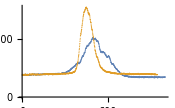
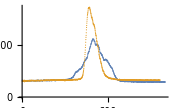
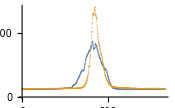
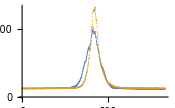
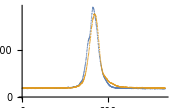
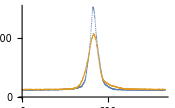
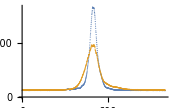
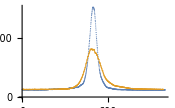

```mathematica
trans=Transpose[#]&/@imd;

xList=Total[#]&/@imd;
yList=Total[#]&/@trans;

xFitEqn=a(Exp[-2((x-x0)/wx)^2])+b;
yFitEqn=a(Exp[-2((y-y0)/wy)^2])+b;

xFitVars={{x0,window(*+200*)(*900*)},{wx,100},{a,50*(2 window+1)},{b,0}};
yFitVars={{y0,window(*+100*)(*700*)},{wy,100},{a,50*(2 window+1)},{b,0}};

xFit=NonlinearModelFit[#,xFitEqn,xFitVars,x]&/@xList;
yFit=NonlinearModelFit[#,yFitEqn,yFitVars,y]&/@yList;

xFitParams=#["ParameterTable"]&/@xFit//Quiet
yFitParams=#["ParameterTable"]&/@yFit//Quiet

{x0Fit,wxFit,axFit,bxFit}=Transpose[#[[1,1,2;; ,2]]&/@xFitParams];
{y0Fit,wyFit,ayFit,byFit}=Transpose[#[[1,1,2;; ,2]]&/@yFitParams];

Table[
Show[
ListPlot[{xList[[i]],yList[[i]]},PlotRange->Full,ImageSize->175]

(*,Plot[{xFit[[i]][x],yFit[[i]][x]},{x,0,2 window+1}]*)
]
,{i,1,Length[xList]}]
```

w_x = {730.527, 629.481, 534.203, 414.925, 317.451, 253.878, 225.506, 237.381, 270.45, 308.444, 382.634, 429.024, 450.758, 511.912, 563.806, 631.913, 607.362}μm

w_y = {350.278, 309.149, 274.355, 257.625, 296.117, 333.211, 392.078, 466.074, 534.821, 596.601, 650.878, 719.452, 788.399, 870.822, 926.339, 994.53, 953.82}μm

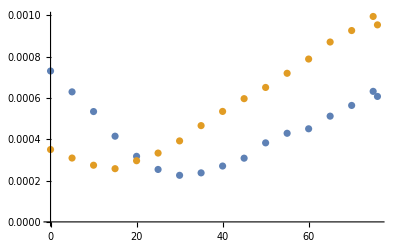

```mathematica
pos=Table[{x1[[i]]+x0Fit[[i]],y1[[i]]+y0Fit[[i]]},{i,1,Length[x0Fit]}];
pos=(#/.{x_,y_}->{x,yDim-y})&/@pos;

pixelWidth=4.4*^-6;(*length per pixel for pixelink camera*)
(*pos=pixelWidth*pos;*)

wxFitm=pixelWidth*wxFit;
wyFitm=pixelWidth*wyFit;

"w_x = "<>ToString[10^6 wxFitm]<>"μm"
"w_y = "<>ToString[10^6 wyFitm]<>"μm"

ListPlot[pos,PlotRange->{{0,xDim},{0,yDim}}];
position=Append[Range[0,75,5],76];
ListPlot[{Table[{position[[j]],wxFitm[[j]]},{j,1,Length[position]}],Table[{position[[j]],wyFitm[[j]]},{j,1,Length[position]}]}]
```

```mathematica
(*Not with current LaserData values*)
h = 6.62607 10^-34;  (*Planck constant*)
c = 299792458;  (*Speed of light*)
Γ1 =95 10^6; (*s^-1 Partial linewidth/Einstein A coefficient for 6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition from NIST database*)
Γ2 =31 10^6; (*s^-1 Partial linewidth/Einstein A coefficient for 5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition from NIST database*)
λc=493.4 10^-9;
λr=649.7 10^-9;

(*beamPower=20.0 10^-3;
wxFitMean=Mean[wxFitm];
wyFitMean=Mean[wyFitm];

I0=(2 beamPower)/(π wxFitMean wyFitMean)
"W/m^2"
*)
Isatc=π/3(h c Γ1)/λc^3;(*very approximate; W/m^2*)
Isatr=π/3(h c Γ2)/λr^3;(*very approximate; W/m^2*)
Ic=(((5.322+4.35+2.87) 10^-3)/3)/(π/3((363.459 381.642+370.581 378.337)/2+(568.204 510.631+532.291 512.408)/2+370.581 378.337)10^-12);(*5.322 10^-3 W prepass, 4.35 10^-3 W pass, 2.87 10^-3 W postpass*)
Ir=(((2.707+2.22+1.719)10^-3)/3)/(π/3((638.964 619.672+592.883 607.873)/2+(866.126 941.278+823.464 975.921)/2+403.974 474.128)10^-12);(*2.707 10^-3 W prepass, 2.22 10^-3 W pass, 1.719 10^-3 W postpass*)
ΩC=√(Ic/Isatc Γ1^2/2)
ΩR=√(Ir/Isatr Γ2^2/2)
ΩC/(2π 10^6)
ΩR/(2π 10^6)

ΩCfunc[Ic]/(√3)
ΩRfunc[Ir]/(√3)
```

4.41751×10^8

1.77044×10^8

70.3069

28.1774

2.55045×10^8

1.02216×10^8

```mathematica
filelist={"coolingpass1.jpg","coolingpass2.jpg","coolingpostpass1.jpg","coolingpostpass2.jpg","coolingprepass1.jpg","repumppass1.jpg","repumppass2.jpg","repumppostpass1.jpg","repumppostpass2.jpg","repumpprepass1.jpg"};
Subscript[w, x] = {363.459, 370.581, 568.204, 532.291, 370.581, 638.964, 592.883, 866.126, 823.464, 403.974};
Subscript[w, y] = {381.642, 378.337, 510.631, 512.408, 378.337, 619.672, 607.873, 941.278, 975.921, 474.128};
For[i=1,i≤ Length[filelist],i++,Print["For the file ",filelist[[i]]," the waist in the x direction is ",Subscript[w, x][[i]]," μm and in the y direction it is ",Subscript[w, y][[i]]," μm."]]
```

For the file coolingpass1.jpg the waist in the x direction is 363.459 μm and in the y direction it is 381.642 μm.

For the file coolingpass2.jpg the waist in the x direction is 370.581 μm and in the y direction it is 378.337 μm.

For the file coolingpostpass1.jpg the waist in the x direction is 568.204 μm and in the y direction it is 510.631 μm.

For the file coolingpostpass2.jpg the waist in the x direction is 532.291 μm and in the y direction it is 512.408 μm.

For the file coolingprepass1.jpg the waist in the x direction is 370.581 μm and in the y direction it is 378.337 μm.

For the file repumppass1.jpg the waist in the x direction is 638.964 μm and in the y direction it is 619.672 μm.

For the file repumppass2.jpg the waist in the x direction is 592.883 μm and in the y direction it is 607.873 μm.

For the file repumppostpass1.jpg the waist in the x direction is 866.126 μm and in the y direction it is 941.278 μm.

For the file repumppostpass2.jpg the waist in the x direction is 823.464 μm and in the y direction it is 975.921 μm.

For the file repumpprepass1.jpg the waist in the x direction is 403.974 μm and in the y direction it is 474.128 μm.

```mathematica
mag1={2,2.068259385665529,2.156996587030717,2.2389078498293515,2.3003412969283277,2.3890784982935154,2.5051194539249146,2.6552901023890785,2.7713310580204777,2.887372013651877,3.0307167235494883,3.180887372013652,3.324232081911263,3.48122866894198,3.631399317406143,3.7952218430034135,3.9385665529010243,4.061433447098977};
angle1={-20.275590551181104,-21.336567144124047,-22.633159549595554,-23.575622799709762,-24.164360001074954,-24.988511461664558,-26.166187417699064,-27.224745370992444,-28.284311090806483,-29.107656338179574,-29.812085136115662,-30.87064308940905,-31.456961651124672,-32.042877106232034,-32.74710435086399,-33.332818252667224,-33.919136814382846,-34.15172932734944};
mag2={2,2.1365187713310583,2.25938566552901,2.3754266211604094,2.5119453924914676,2.621160409556314,2.7713310580204777,2.9965870307167237,3.174061433447099,3.392491467576792,3.6245733788395906,3.8225255972696246,4,4.21160409556314,4.354948805460751};
angle2={-6.338582677165352,-5.389669721318963,-4.559270108301309,-4.083402757249196,-3.252600037623285,-2.658824003654832,-1.8276181774206535,-0.8760850286205706,-0.1621832253903417,0.5529278976646683,1.2684421273279405,1.8648383542500877,2.3425196850393704,2.5849883099083595,2.7073311655155745};
```

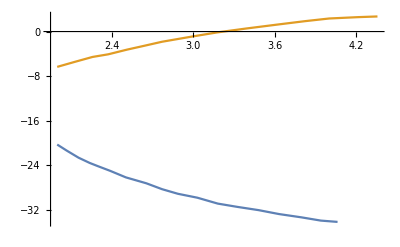

```mathematica
ListLinePlot[{Table[{mag1[[i]],angle1[[i]]},{i,1,Length[mag1]}],Table[{mag2[[j]],angle2[[j]]},{j,1,Length[mag2]}]}]
```